# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\LMG

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);

Clear[F];
F[J_,α_,k_,τ_]:=MatrixExp[N[(-I*k/(2J))(Sx[J].Sx[J])]].MatrixExp[(-I*α*τ)(Sz[J])];

Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];
```

```mathematica
radius=1.99999;
delta=0.035;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

10452

```mathematica
radius=0.6;
delta=0.01;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
region=gridPoints;
region//Length
```

14641

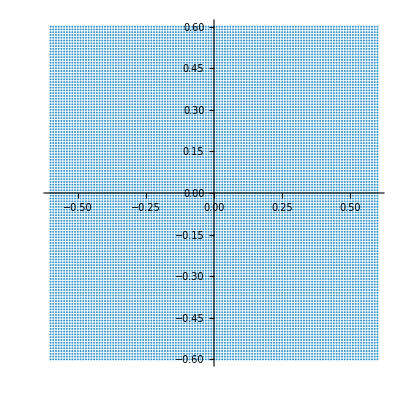

```mathematica
ListPlot[region,AspectRatio->1]
```

## LMG

```mathematica
Clear[Hlmg, floq];
Hlmg[J_]:=Hlmg[J]=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
```

```mathematica
Clear[gx,gy];
gx=-15/10;
gy=1/gx;
```

```mathematica
Clear[lipmatm,lipmatM];
J=100;
mat2=Hlmg[J];
(*mat2=ConjugateTranspose[rotation].Hlmg[J].rotation;*)
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

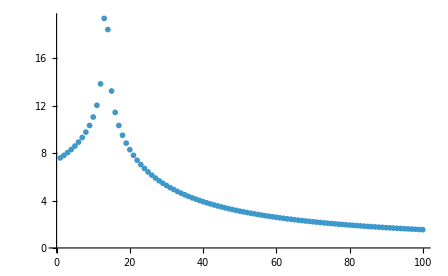

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All]
(*ListPlot[(2Pi)/Differences[Chop[lipeigenvalm]],PlotRange->All]*)
```

```mathematica
ListDensityPlot[newd2Mlmg,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2 +, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

## Husimis

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Quiet[Abs[Conjugate[cohes[[i]]].ψ]^2]},{i,Length[region]}];
```

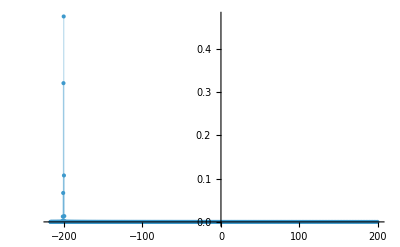

```mathematica
Clear[lipmatm,lipmatM];
J=200;
mat2=Hlmg[J];
(*mat2=ConjugateTranspose[rotation].Hlmg[J].rotation;*)
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
ini=a2[J,0,0];
inieigen=Normalize[Conjugate[lipneweigenvec].ini];
ListPlot[Transpose[{lipneweigenval,Abs[inieigen]^2}],PlotRange->All,Filling->Axis]
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
data=SortBy[Transpose[{Abs[inieigen]^2,lipneweigenvec}],First];
Do[

Export["Eigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>", dq_"<>ToString[delta]<>".png",ListDensityPlot[husimi[data[[i]][[2]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["Eigenvec +"<>ToString[i]<>", J = "<>ToString[J]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,-10,-1,1}]
```